### Fit P(t)=C exp(-t/T_2)

```mathematica
distr00={{1,90.0},{5,83.5},{10,82.1},{15,78.9},{20,74.6},{25,70.6},{30,68.4},{35,65.7},{40,61.0},{45,60.2},{50,52.9},{55,53.6},{60,49.4},{65,43.2},{70,43.7},{74,42.3}};
Pt1=C1 Exp[-t/T2];
fit1=FindFit[distr00,Pt1,{C1,T2},t]
```

{C1→90.9493,T2→98.2161}

```mathematica
Pf1=Function[{t},Evaluate[Pt1/.fit1]]
```

Function[{t},90.9493 ⅇ^(-0.0101816 t)]

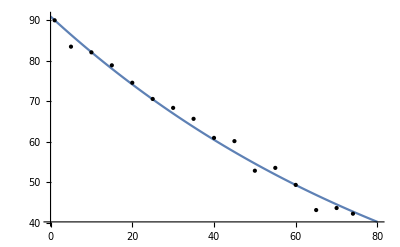

```mathematica
Plot[Pf1[t],{t,0,80},Epilog->Map[Point,distr00]]
```

### Fit P(t)=C exp[-(t/T_2)^2]

```mathematica
Pt2=C2 Exp[-(t/T2b)^2];
fit2=FindFit[distr00,Pt2,{C2,T2b},t]
```

{C2→81.4169,T2b→83.6089}

```mathematica
Pf2=Function[{t},Evaluate[Pt2/.fit2]]
```

Function[{t},81.4169 ⅇ^(-0.000143052 t^2)]

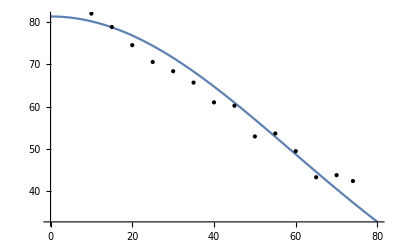

```mathematica
Plot[Pf2[t],{t,0,80},Epilog->Map[Point,distr00]]
```